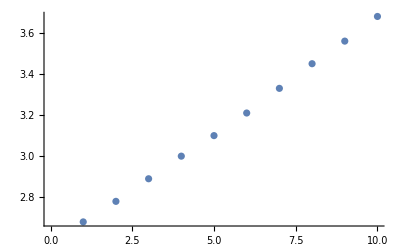

```mathematica
r={2.68,2.78,2.89,3.00,3.10,3.21,3.33,3.45,3.56,3.68};
data=Table[{i,r[[i]]},{i,1,10}];
pd=ListPlot[data]
```

```mathematica
fd=Fit[data,{1,x},x]
```

2.556+0.111273 x

```mathematica
Needs["LinearRegression`"]
```

General::obspkg: "LinearRegression`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

RegressionReport::shdw: Symbol "RegressionReport" appears in multiple contexts {"RegressionCommon`", "Global`"}; definitions in context "RegressionCommon`" may shadow or be shadowed by other definitions.

RSquared::shdw: Symbol "RSquared" appears in multiple contexts {"RegressionCommon`", "Global`"}; definitions in context "RegressionCommon`" may shadow or be shadowed by other definitions.

Regress::shdw: Symbol "Regress" appears in multiple contexts {"LinearRegression`", "Global`"}; definitions in context "LinearRegression`" may shadow or be shadowed by other definitions.

```mathematica
Regress[data,{1,x},x,RegressionReport->{RSquared}]
```

{RSquared→0.999338}

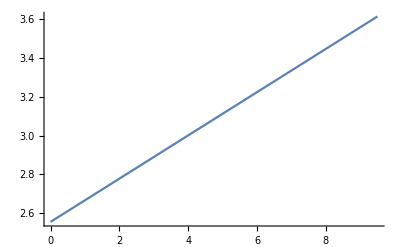

```mathematica
Plot[fd,{x,0,9.5}]
```

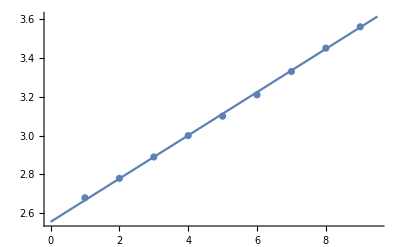

```mathematica
Show[%,pd]
```

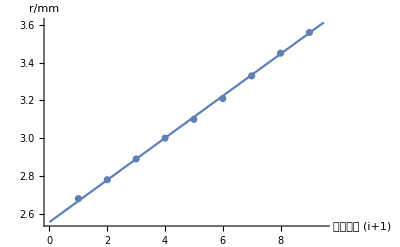

```mathematica
Show[%14,AxesLabel->{HoldForm[砝码个数 (i+1)],HoldForm[r/mm]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

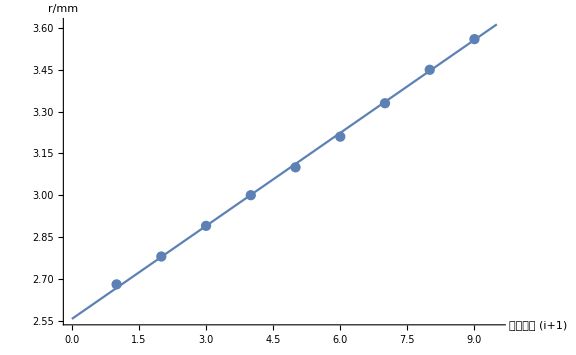

```mathematica
Show[%17,ImageSize->Large]
```

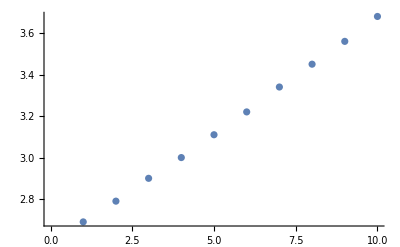

```mathematica
r'={2.69,2.79,2.90,3.00,3.11,3.22,3.34,3.45,3.56,3.68};
data2=Table[{i,r'[[i]]},{i,1,10}];
pd2=ListPlot[data2]
```

```mathematica
fd2=Fit[data2,{1,x},x]
```

2.568+0.110182 x

```mathematica
Regress[data2,{1,x},x,RegressionReport->{RSquared}]
```

{RSquared→0.999514}

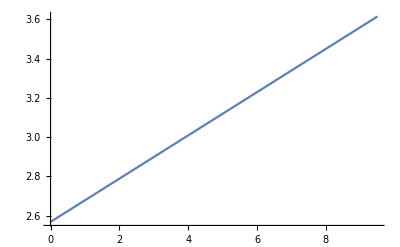

```mathematica
Plot[fd2,{x,0,9.5}]
```

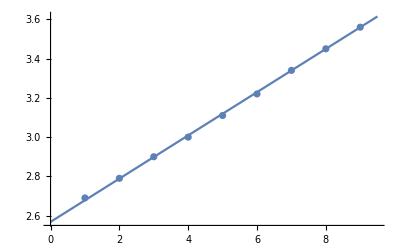

```mathematica
Show[%,pd2]
```

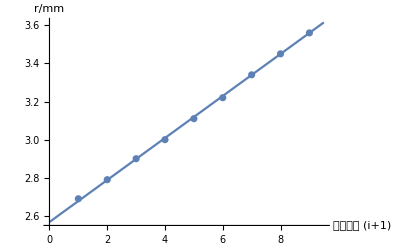

```mathematica
Show[%29,AxesLabel->{HoldForm[砝码个数 (i+1)],HoldForm[r/mm]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

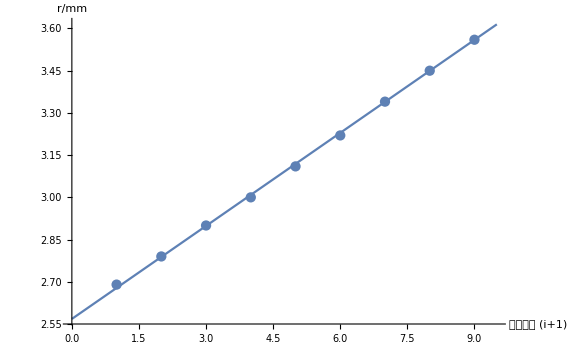

```mathematica
Show[%30,ImageSize->Large]
```